## Kapitola 12 - Hopfieldova síť a umělé vzory

Demonstrace použití Hopfieldovy neuronové sítě k rozpoznávání umělých dat.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Vytvoření vstupních vzorů

Vytvoříme si umělé vzory - číslice 1, 2 a 3.

```mathematica
x={{{-1,-1,-1,1,1,-1,-1,-1},{-1,-1,-1,1,1,-1,-1,-1},{-1,-1,-1,1,1,-1,-1,-1},{-1,-1,-1,1,1,-1,-1,-1},{-1,-1,-1,1,1,-1,-1,-1},{-1,-1,-1,1,1,-1,-1,-1},{-1,-1,-1,1,1,-1,-1,-1},{-1,-1,-1,1,1,-1,-1,-1}},{{1,1,1,1,1,1,-1,-1},{-1,-1,-1,-1,1,1,-1,-1},{-1,-1,-1,-1,1,1,-1,-1},{1,1,1,1,1,1,-1,-1},{1,1,1,1,1,1,-1,-1},{1,1,-1,-1,-1,-1,-1,-1},{1,1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,1,-1,-1}},{{-1,-1,1,1,1,1,-1,-1},{-1,-1,-1,-1,-1,-1,1,-1},{-1,-1,-1,-1,-1,1,-1,-1},{-1,-1,-1,1,1,-1,-1,-1},{-1,-1,-1,-1,-1,1,-1,-1},{-1,-1,-1,-1,-1,-1,1,-1},{-1,-1,-1,-1,-1,-1,1,-1},{-1,-1,1,1,1,1,-1,-1}}};
```

Takto vypadají naše vzory :

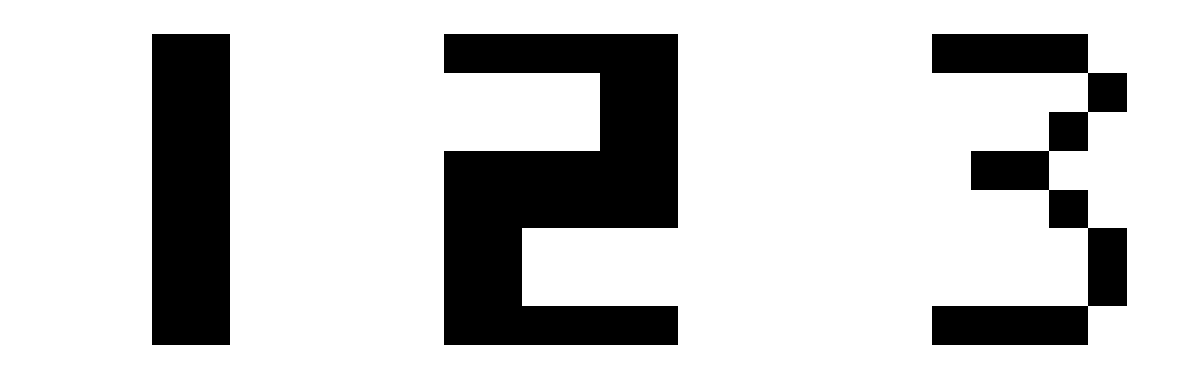

```mathematica
GraphicsGrid[{Map[ArrayPlot[#+1,DisplayFunction->Identity,FrameTicks->None]&,x]}]
```

Před inicializací Hopfieldovy sítě je potřeba převést matice na vektory.

```mathematica
y=Map[Flatten,x,{1}];
```

## Zpracování dat neuronovou sítí

Inicializace sítě - síť bude mít 64 neuronů (vstupy velikosti 8 x 8 = 64). Vytvořenou síť si uložíme do proměnné "net".

```mathematica
net=HopfieldFit[y]
```

Hopfield[W,{NetType → Discrete, CreationDate → {2011, 5, 3, 23, 9, 43.9777571}}]

Vygenerujeme si zašuměné testovací vzory.

```mathematica
sum=Table[If[RandomReal[]<0.85,1,-1],{3},{64}]
```

{{1,1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,1,1,1,1,1,1,1,1,1,-1,1,1,1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,-1,1,1,1,1,1,1,-1,1,1,1,1,1},{1,1,1,-1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,1,1,1,1,1,-1,1,-1,-1,1,-1,1,1,1,1,1,-1,1,1,1,1,1,1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1},{1,1,-1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,1,1,1,-1,1,1,1,1,1,-1,-1,1,1,1,1,1,1,1}}

Takto vypadají vygenerované zašuměné vzory.

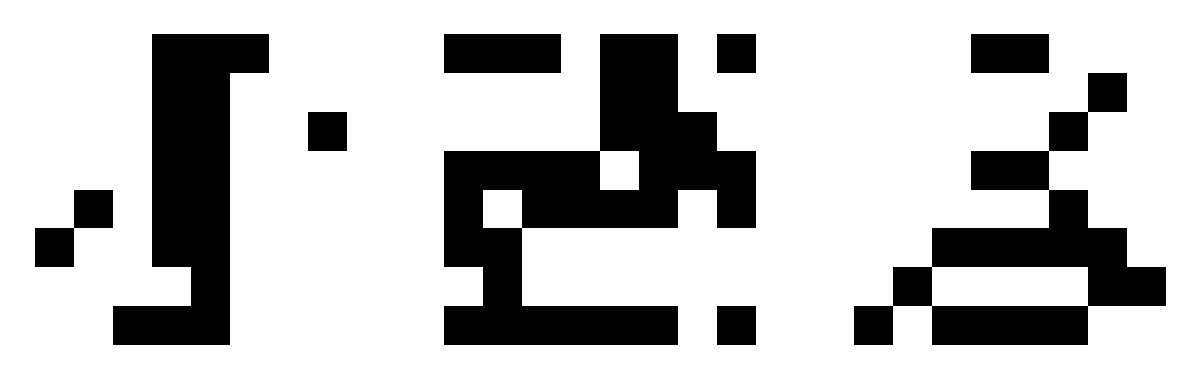

```mathematica
sumMap=Map[Partition[#,8]&,sum*y,1];
GraphicsGrid[{Map[ArrayPlot[#+1,DisplayFunction->Identity,FrameTicks->None]&,sumMap]}]
```

Nyní použijeme vygenerovaná data na natrénovanou síť a zobrazíme si její odpověď.

```mathematica
net[Map[Flatten,sumMap]];
GraphicsGrid[{Map[ArrayPlot[#+1,DisplayFunction->Identity,FrameTicks->None]&,Map[Partition[#,8]&,%,1]]}]
```

-Graphics-

Může se objevit inverzní obraz, to je dáno tím, že jeho vektor také tvoří minimální energetickou funkci.

Generování zašumněných vzorů můžete vyhodnotit několikrát a podívat se jak síť reaguje na různě zašumněné vzory.

Funkcí NetPlot lze zobrazit pokles energetické funkce a její trajektorii.

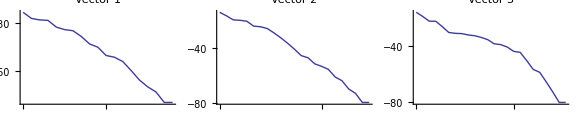

```mathematica
NetPlot[net,sum,DataFormat->Energy]
```

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011. Vznikl úpravou textu Petra Chlumského.